```mathematica
(*Tutorial e introducción para utilizar bien mathematica*)

(*Para asignar una variable es con el igual y para que no se muestre se utiliza ;*)
b=4;
```

```mathematica
(*Las operaciones básicas*)
```

```mathematica
c=b^2+b -4*b +1/b
```

17/4

```mathematica
(*Para redondear los numero utilizamos la función 'N', los numeros reales mas utilizados es E (numero e) y Pi (numero pi)*)
N[E,10]
```

2.718281828

```mathematica
k=2+E+Pi
N[k]
```

7.85987

```mathematica
(*Para escribir con formulas y latex hay que utilizar la paleta y luego en asistencia de esciruta o matematica *)
```

# Hola Mari carmen

Aqui vamos a escribir diabluras  ∫cos(z)ⅆz

```mathematica
(*Para simplicar ecuaciones utilizamos simplify, utilizar asistende de clase, importante los espacios entre x e y*)
Simplify[((4x y-2x y) (5 x^3-y^2))/x]
```

-2 y (-5 x^3+y^2)

```mathematica
(*Fuciones básicas*)
Abs[2-I 10]
(*El numero complejo se escribe con la letra I*)

Sign[-1]
Round[4.5]
```

```mathematica
Floor[2.7]

Ceiling[3.1]

(*PAra borrar un valor*)
Clear[c]
```

(√(3/2))/2

0.61

(√3)/2

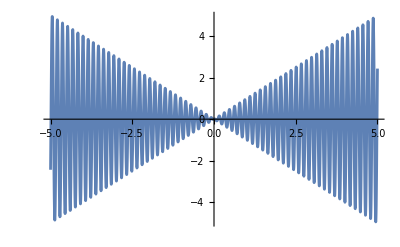

```mathematica
c=Sin[Pi/3]*Cos[Pi/4]
N[c,2]
Cos[30 Degree]

(*Graficar utilizamos la función Plot*)

Plot[x*Cos[40*x],{x,-5,5}]
```

```mathematica
(*Resolver ecuaciones, utilizar Solve*)
Solve[x^3-2x+1 ==0, x]
(*Se pone un doble igual y la variable a la derecha con la coma, para varias variables se utiliza {}*)
a=3;b=2;
Solve[{a*x+2*y==2,b*y-x==0},{x,y}]
(*De forma matricial, utilizar asistente de matematica basica y utilizar el punto para multiplicar la patriz*)
Solve[({{1, 2, 0, 0}, {1, 2, 3, 0}, {0, 2, 4, 5}, {0, 0, 3, 5}}).({{x}, {y}, {z}, {t}})==({{0}, {0}, {1}, {0}}),{x,y,z,t}]
```

{{x→1},{x→1/2 (-1-√5)},{x→1/2 (-1+√5)}}

{{x→1/2,y→1/4}}

{{x→-1,y→1/2,z→0,t→0}}

```mathematica
(*Para hacerlo de forma numérica*)
NSolve[{1.5*x+2*y==2,2.7*y-x==0},{x,y}]
```

{{x→0.892562,y→0.330579}}

1-x^2/6+x^4/120+O[x]^5

1-x^2/6+x^4/120-x^6/5040+x^8/362880-x^10/39916800

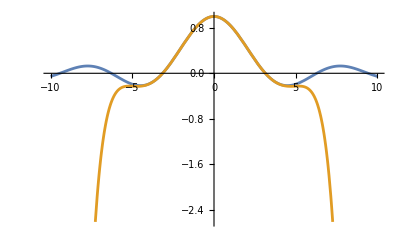

```mathematica
(*La serie de Taylor alrededor de un punto*)
Series[Sin[x]/x,{x,0,4}]
(*En el corchete {} el segundo espacio es para el punto donde se hacer el desarrollo y luego el tercer espacio es el orden del delsarrollo*)

(*PAra quitar el error utilizamos Normal*)
y=Normal[Series[Sin[x]/x,{x,0,10}]]
(*Para graficar varias funciones en el mismo plot añadimos llaves {}*)
Plot[{Sin[x]/x,y},{x,-10,10}]
```

```mathematica
(*Para las derivadas utilizar ayudante de clase*)
D[(5x^2-2 z), x];
D[x^2+x-z,x];
(*Para segundas y terveras derivadas, en el segundo hueco de {}será el orden de la derivada*)
D[x^3-x^2,{x,2}];
(*Para funciones se define la funcion*)

f[x_]:= Cos[x^2+2x+1];
(*Se puede utilizar las comas para las derivadas*)
f'[x];

(*Para las integrales utilizar asistende de clase*)
∫_0^(2 Pi) Cos[x]^2ⅆx;
```

```mathematica
(*Para crear un array*)

Lista={1,4,2,6,3,9};
(*Para que me de el valor en la posicion que quiero*)
Lista[[2]];
(*Numero de elementos*)
n=Length[Lista];
For[i=1,i<n,i++,Print[Lista[[i]]]]
```

1

4

2

6

3